# Adding the temperature-size rule to temperature-dependent consumer-resource models

## MST group project

## Recreating Gilbert

Equations 1 and 2 from Gilbert et al 2014 (with potential temperature dependencies added)

```mathematica
dRdt[R_,C_,T_]:=r[T] R(1-R/K[T])-f[R,T] R C;
dCdt[R_,C_,T_]:=e f[R,T]R C-m[C,T]C;
```

where R is biomass of resource, C is biomass of consumer, T is temperature, K is resource carrying capacity, f is the functional response, e is the conversion efficiency of resources into new consumers, and m is consumer mortality.

BCR at a given T, as defined by Gilbert (Eqn 5),

```mathematica
BCR[T_]:=(e a[T]K[T])/m[T]
```

Equilibrium biomasses at given temperature assuming a type I functional response and density-independent consumer mortality (as in most of Gilbert)

```mathematica
Eq[T_]:=Solve[{0==dRdt[R,C,T],0==dCdt[R,C,T]}/.f[R,T]->a[T]/.m[C,T]->m[T],{R,C}]
```

Equilibrium consumer to resource biomass ratio at a given temperature (at the equilibrium where both populations persist)

```mathematica
CR[T_]:=C/R/.Eq[T][[3]]
```

The Jacobian evaluated at equilibrium (determines stability)

```mathematica
Jac={{D[dRdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],R],D[dRdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],C]},{D[dCdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],R],D[dCdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],C]}}/.Eq[T][[3]];
```

The eigenvalues of the Jacobian are

```mathematica
lambda=Eigenvalues[Jac];
```

Use Table 1 of Gilbert. Want K=100 at 15 degrees C (Figure 3 of Gilbert), so we need K0 to be

```mathematica
K15=Solve[100==K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T/.T->273.15+15,K0];
```

Figure 3a of Gilbert (same shape but numbers too large)

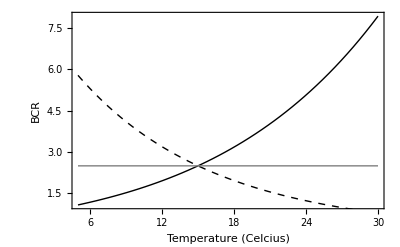

```mathematica
Show[
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thick}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.32,{T,5,30},PlotStyle->{Black,Thick,Dashed}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Figure 3b of Gilbert (off by factor of 3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

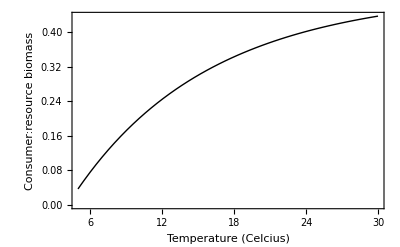

```mathematica
Show[Plot[ CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"}
]
```

Figure 3c of Gilbert

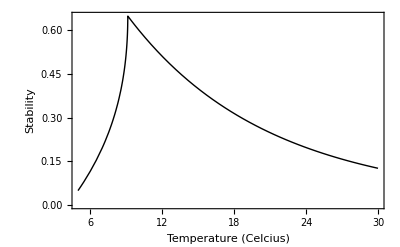

```mathematica
Show[Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9]],{T,5,30},PlotStyle->{Black,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"}
]
```

## Adding mass to Gilbert

Now we want to add the body mass relations given in Table 1 of DeLong et al. 2015.

Temperature dependencies of rates given in Table 1 of Gilbert et al. (now letting the constant depend on body mass M)

```mathematica
cr={C,R};
GilbertTable1={
r[T]->r[M] Exp[-EB/(k T[R])],
K[T]->K[M] Exp[EB/(k T[R])-ES/(k T[S])],
m[T]->m[M] Exp[-Em/(k T[C])],
a[T]->a[M] Sqrt[Sum[(ν0[cr[[i]]] Exp[-Eν[cr[[i]]]/(k T[cr[[i]]])])^2,{i,1,Length[cr]}]],
e->e[M]
};
```

Body mass dependencies from DeLong et al.

```mathematica
DeLongTable1={
r[M]->r0 M[R]^ρ,
K[M]->K0 M[R]^κ,
a[M]->a0 M[C]^α,
e[M]->e0 M[C]^ϵ,
m[M]->m0 M[C]^μ
};
```

The temperature-size rule (from Forster et al. 2012), for unicells (e.g., algae)

```mathematica
TSR=M[i_]->M15(1-0.02 (T-15));
```

What does mass at 15 C need to be to have K=100 at T=15 C (to stay consistent with Gilbert)

```mathematica
m15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.k->8.62*10^-5/.κ->-0.81/.EB->0.32/.ES->0.9/.TSR/.T->15]
```

{{M15→1.02553×10^-15 K0^(100/81)}}

Figure 3a of Gilbert (new predictions in red; new dashed curve and horizontal line are now on the order of 10^10 and 10^20 and so do not appear in plot)

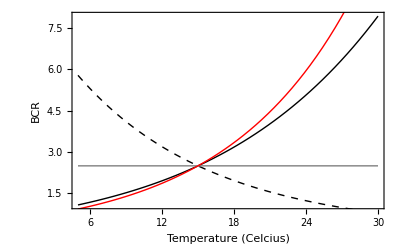

```mathematica
Show[
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thick}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.32,{T,5,30},PlotStyle->{Black,Thick,Dashed}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thick}],
Plot[Simplify[BCR[T]/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.k->8.62*10^-5/.κ->-0.81/.TSR/.m15/.EB->0.32/.ES->0.9,K0>0],{T,5,30},PlotStyle->{Red,Thick}],
Plot[Simplify[BCR[T]/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.k->8.62*10^-5/.κ->-0.81/.TSR/.m15/.EB->0.9/.ES->0.32,K0>0],{T,5,30},PlotStyle->{Red,Thick,Dashed}],
Plot[Simplify[BCR[T]/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.k->8.62*10^-5/.κ->-0.81/.TSR/.m15/.EB->0.9/.ES->0.9,K0>0],{T,5,30},PlotStyle->{Pink,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Figure 3b of Gilbert (new prediction in red)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

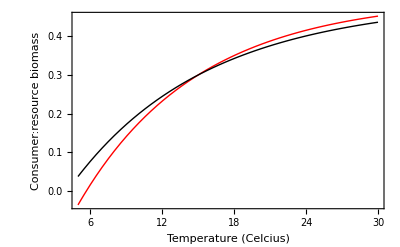

```mathematica
Show[
Plot[Simplify[CR[T]/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.k->8.62*10^-5/.κ->-0.81/.TSR/.m15/.EB->0.32/.ES->0.9,K0>0],{T,5,30},PlotStyle->{Red,Thick}],
Plot[  CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"}
]
```

Figure 3c of Gilbert

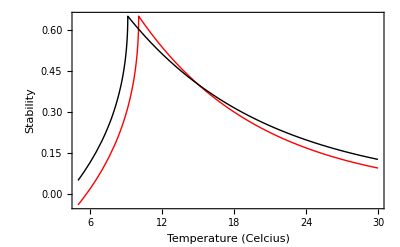

```mathematica
Show[Plot[-Max[Re[Simplify[lambda/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.GilbertTable1/.DeLongTable1/.T[i_]->T+273.15/.k->8.62*10^-5/.κ->-0.81/.TSR/.m15/.EB->0.32/.ES->0.9,K0>0]]],{T,5,30},PlotStyle->{Red,Thick}],Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9]],{T,5,30},PlotStyle->{Black,Thick}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"}
]
```

This only looks at temperature and body mass dependencies in resource carrying capacity K. We next add temperature and mass dependencies to the other rates (and temperature dependence in consumer body mass) to see if this gives bigger discrepancies between the two models.

## All the dependencies

Let the temperature size rule be linear, but potentially different for resource and consumer

```mathematica
Clear[TSR]
TSR=M[i_]->M15[i](1-β[i](T[i]-(273.15+15)));
```

where M15[i] is the mass of the resource of consumer, i={R,C}, at 15 degrees celcius, β[i] is the percent decline in body size with a degree increase in temperature, and T is the current temperature in Kelvins.

To have the same population dynamics parameter values at 15 degrees as we did above with the TSR only in K, we need

```mathematica
a15=Solve[0.1==a[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,a0]//Flatten
```

{a0→(0.1 M15[C]^(-1. α))/(√(ⅇ^(-(0.00694083 Eν[C])/k) ν0[C]^2+ⅇ^(-(0.00694083 Eν[R])/k) ν0[R]^2))}

```mathematica
e15=Solve[0.15==e[M]/.DeLongTable1/.TSR/.T[i_]->273.15+15,e0]//Flatten
```

{e0→0.15 M15[C]^(-1. ϵ)}

```mathematica
k15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten
```

{K0→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k) M15[R]^(-1. κ)}

```mathematica
r15=Solve[2==r[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,r0]//Flatten
```

{r0→2. ⅇ^((0.00347041 EB)/k) M15[R]^(-1. ρ)}

```mathematica
m15=Solve[0.6==m[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,m0]//Flatten
```

{m0→0.6 ⅇ^((0.00347041 Em)/k) M15[C]^(-1. μ)}

Now, BCR as a function of temperature is

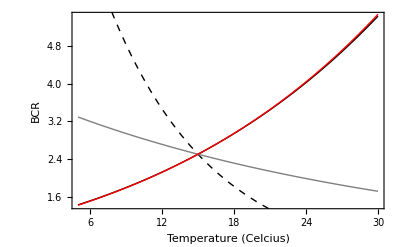

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.M15[R]->1/.M15[C]->2/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.M15[R]->1/.M15[C]->2/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Black,Dashed}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.M15[R]->1/.M15[C]->2/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.M15[R]->1/.M15[C]->2/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Red}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","BCR"}
]
```

Nothing much doing here.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

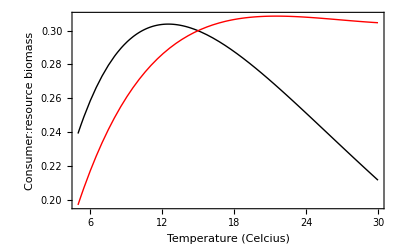

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.M15[R]->1/.M15[C]->2/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thick},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.M15[R]->1/.M15[C]->2/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thick},Axes->False],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Consumer:resource biomass"},
PlotRange->All
]
```

NOTE: with the TSR, increasing temperature no longer changes the ratio of consumer to resource biomass ratio!!!!!

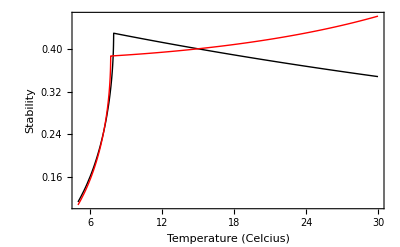

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.M15[R]->1/.M15[C]->2/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thick},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.M15[R]->1/.M15[C]->2/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thick},PlotRange->{0,All}],
Frame->True,
FrameLabel->{"Temperature (Celcius)","Stability"},
PlotRange->All
]
```

NOTE: with the TSR, increasing temperature no destabilizes coexistence, instead stability increases!!!